```mathematica
real={0.5018 ,2.53,
0.7001 ,1.967,
0.8988, 1.476,
1.0978 ,1.0184,
1.2971, 0.6693,
1.4964 ,0.403,
1.6959, 0.2304,
1.8955, 0.13008,
2.1381 ,0.06169,
2.4379, 0.02362,
2.7786 ,0.007775,
3.1788 ,0.002195,
3.6176 ,0.0005282,
4.1183, 0.00010865,
4.6558, 2.103*10^-5,
5.3864, 3.892*10^-6};
```

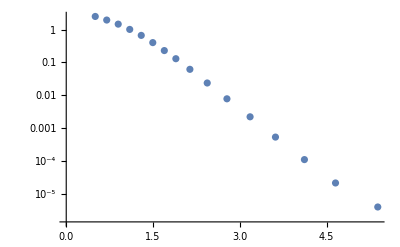

```mathematica
realplot=ListLogPlot[Table[{real[[2i-1]],real[[2i]]},{i,1,16}]]
```

reverse slope T=0.249,Ts=0.327,cS=8.6,cT=38.4,error=  0.391206829321445

```mathematica
SetDirectory["C:\\Users\\86177\\Desktop\\innovation\\program\\lambda\\lambda"]
```

C:\Users\86177\Desktop\innovation\program\lambda\lambda

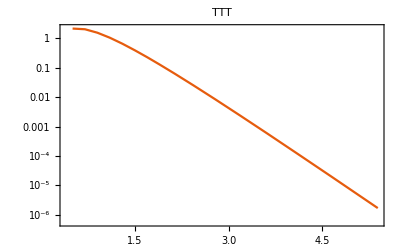
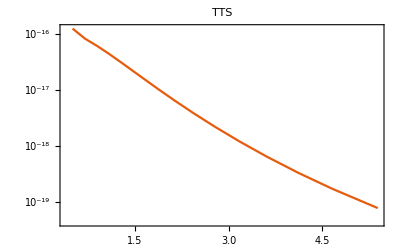
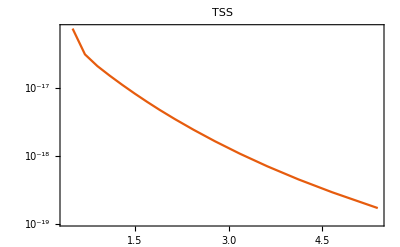
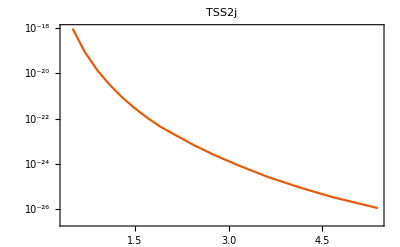
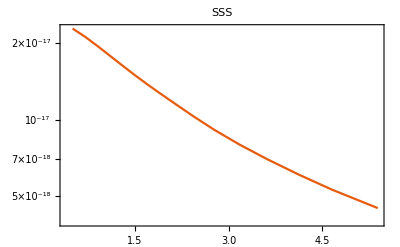
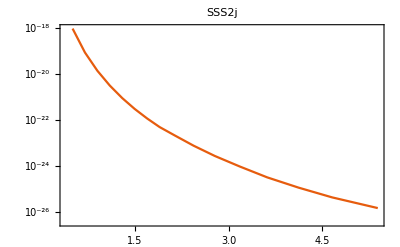
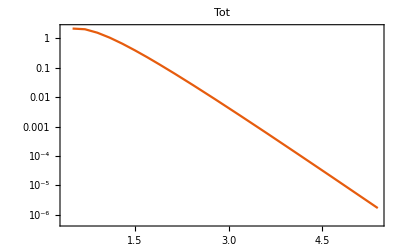

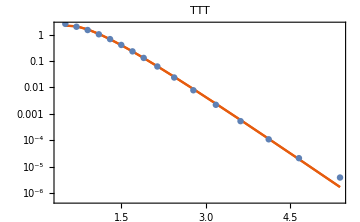

```mathematica
"          %pt           TTT           TTS           TSS           TSS2j           SSS           SSS2j           Tot\n        0.502    2.15604E+00    1.26342E-16    7.39798E-17    9.15662E-19    2.28879E-17    9.14265E-19    2.15604E+00\n        0.700    2.04490E+00    8.35116E-17    3.09453E-17    8.32188E-20    2.12578E-17    8.36001E-20    2.04490E+00\n        0.899    1.55797E+00    6.12669E-17    2.08442E-17    1.33375E-20    1.95435E-17    1.35005E-20    1.55797E+00\n        1.098    1.05346E+00    4.35541E-17    1.50441E-17    3.00803E-21    1.78887E-17    3.07080E-21    1.05346E+00\n        1.297    6.61624E-01    3.03143E-17    1.10632E-17    8.53765E-22    1.63654E-17    8.79581E-22    6.61624E-01\n        1.496    3.95876E-01    2.09253E-17    8.24456E-18    2.86577E-22    1.50010E-17    2.98084E-22    3.95876E-01\n        1.696    2.28888E-01    1.44359E-17    6.22144E-18    1.09182E-22    1.37932E-17    1.14695E-22    2.28888E-01\n        1.895    1.29107E-01    1.00051E-17    4.75434E-18    4.59801E-23    1.27303E-17    4.87941E-23    1.29107E-01\n        2.138    6.28390E-02    6.47795E-18    3.48674E-18    1.95207E-23    1.15686E-17    2.10650E-23    6.28390E-02\n        2.438    2.51339E-02    3.86432E-18    2.42853E-18    6.93081E-24    1.02944E-17    7.60647E-24    2.51339E-02\n        2.779    8.65054E-03    2.21342E-18    1.65020E-18    2.42710E-24    9.08414E-18    2.71413E-24    8.65054E-03\n        3.179    2.41316E-03    1.19650E-18    1.08289E-18    8.27402E-25    7.95509E-18    9.46478E-25    2.41316E-03\n        3.618    5.83164E-04    6.38450E-19    7.07677E-19    2.75269E-25    6.97354E-18    3.19822E-25    5.83164E-04\n        4.118    1.13316E-04    3.29613E-19    4.54181E-19    9.65341E-26    6.07019E-18    1.15165E-25    1.13316E-04\n        4.656    1.92473E-05    1.72052E-19    2.94547E-19    3.54118E-26    5.28447E-18    4.34235E-26    1.92473E-05\n        5.386    1.70379E-06    7.74608E-20    1.72615E-19    1.15226E-26    4.47213E-18    1.49235E-26    1.70379E-06";
datalabel=StringSplit[StringTrim[StringSplit[%,"\n"][[1]]]];
datalist=StringReplace[#,"E"->"*10^"]&/@ StringSplit[#,"    "]&/@StringSplit[%%,"\n"][[2;;17]]//ToExpression;
Table[ListLogPlot[Join[Partition[datalist[[All,1]],1],Partition[datalist[[All,i]],1],2],PlotLabel->Style[datalabel[[i]],Hue[N@Log[i]]],Joined->True,PlotTheme->"Scientific",PlotRange->Full,Background->White],{i,2,8}]
Show[{%,realplot},Background->White,AxesStyle->Directive[30,Thick],PlotTheme->"Scientific"]
```

```mathematica
Export["lambda.eps",%]
```

lambda.eps